```mathematica
PacletInstall["/home/as/Fourrier/FindBounce-1.1.0.paclet"]
```

PacletObject[…]

```mathematica
Needs["FindBounce`"]
```

```mathematica
PacletFind["FindBounce"]
```

{PacletObject[…]}

```mathematica
Names["FindBounce`*"]
```

{BounceFunction,BouncePlot,FindBounce}

```mathematica
?FindBounce
?BounceFunction
?BouncePlot
```

### Test Run

```mathematica
lambda=0.3;
epsilon=0.1;

V[h_,s_]:=((h^2-1)^2)/4+((s^2-1)^2)/4+lambda h^2 s^2-epsilon h;

vars={h,s};

phiTrue={0.89427236,0.72122546};
phiFalse={-0.60590553,0.88302157};

dummyPath=Table[{(1-t)*phiFalse[[1]]+t*phiTrue[[1]]+0.25*Sin[Pi*t],(1-t)*phiFalse[[2]]+t*phiTrue[[2]]-0.15*Sin[Pi*t]},{t,0,1,1/30}];

bf=FindBounce[V[h,s],vars,{phiFalse,phiTrue},"FieldPoints"->dummyPath];

bf["Action"]
```

274.487

### Initial Path Modified

```mathematica
Directory[]
```

/home/as

```mathematica
SetDirectory@NotebookDirectory[]
```

/home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier

```mathematica
Get["findbounce_csvK_scan_READY.wl"];
```

Current directory = /home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier

Output file will be = /home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier/findbounce_csvK_scan_results.csv

Methods = {straight,csvK1,csvK2,csvK3,csvK4,csvK5,csvK6,csvK7,csvK8}

N list = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

Time limit per FindBounce call = 120 seconds

============================================

Running FindBounce nphi = 1

Vfalse = 0.

Vtrue  = -0.335501

DeltaV = 0.335501

method = straight

status = failed   action = —   time = 0.0299 s

method = csvK1

status = failed   action = —   time = 0.0201 s

method = csvK2

status = failed   action = —   time = 0.0208 s

method = csvK3

status = failed   action = —   time = 0.0198 s

method = csvK4

status = failed   action = —   time = 0.0213 s

method = csvK5

status = failed   action = —   time = 0.0203 s

method = csvK6

status = failed   action = —   time = 0.0203 s

method = csvK7

status = failed   action = —   time = 0.0203 s

method = csvK8

status = failed   action = —   time = 0.0200 s

============================================

Running FindBounce nphi = 2

Vfalse = 0.

Vtrue  = -1.37135

DeltaV = 1.37135

method = straight

status = ok   action = 17.3478   time = 0.2935 s

method = csvK1

status = failed   action = —   time = 0.0004 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 3

Vfalse = 0.

Vtrue  = -2.46805

DeltaV = 2.46805

method = straight

status = ok   action = 38.7261   time = 0.1011 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 4

Vfalse = 0.

Vtrue  = -0.835294

DeltaV = 0.835294

method = straight

status = ok   action = 1284.47   time = 0.0771 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 5

Vfalse = 0.

Vtrue  = -3.46971

DeltaV = 3.46971

method = straight

status = ok   action = 164.247   time = 0.1336 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 6

Vfalse = 0.

Vtrue  = -3.7323

DeltaV = 3.7323

method = straight

status = ok   action = 310.56   time = 0.1295 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 7

Vfalse = 0.

Vtrue  = -0.80376

DeltaV = 0.80376

method = straight

status = ok   action = 24616.4   time = 0.1191 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 8

Vfalse = 0.

Vtrue  = -3.73111

DeltaV = 3.73111

method = straight

status = ok   action = 1091.88   time = 0.1368 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 9

Vfalse = 0.

Vtrue  = -3.66509

DeltaV = 3.66509

method = straight

status = ok   action = 1919.89   time = 0.1563 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 10

Vfalse = 0.

Vtrue  = -5.60393

DeltaV = 5.60393

method = straight

status = ok   action = 1156.5   time = 0.1848 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 11

Vfalse = 0.

Vtrue  = -7.30705

DeltaV = 7.30705

method = straight

status = ok   action = 937.693   time = 0.2213 s

method = csvK1

status = failed   action = —   time = 0.0000 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 12

Vfalse = 0.

Vtrue  = -4.81274

DeltaV = 4.81274

method = straight

status = ok   action = 3300.97   time = 0.2917 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 13

Vfalse = 0.

Vtrue  = -7.07821

DeltaV = 7.07821

method = straight

status = ok   action = 1982.94   time = 0.4714 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 14

Vfalse = 0.

Vtrue  = -7.52703

DeltaV = 7.52703

method = straight

status = ok   action = 2503.84   time = 0.5296 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 15

Vfalse = 0.

Vtrue  = -4.61349

DeltaV = 4.61349

method = straight

status = ok   action = 11721.9   time = 0.4440 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 16

Vfalse = 0.

Vtrue  = -9.00462

DeltaV = 9.00462

method = straight

status = ok   action = 3038.92   time = 0.5790 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 17

Vfalse = 0.

Vtrue  = -8.61869

DeltaV = 8.61869

method = straight

status = ok   action = 4583.29   time = 0.5654 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 18

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 19

Vfalse = 0.

Vtrue  = -3.82474

DeltaV = 3.82474

method = straight

status = ok   action = 60078.4   time = 0.6053 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 20

Vfalse = 0.

Vtrue  = -9.18465

DeltaV = 9.18465

method = straight

status = ok   action = 8285.   time = 0.7893 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 21

Vfalse = 0.

Vtrue  = -11.122

DeltaV = 11.122

method = straight

status = ok   action = 6279.52   time = 0.8936 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 22

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 23

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 24

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 25

Vfalse = 0.

Vtrue  = -14.3324

DeltaV = 14.3324

method = straight

status = ok   action = 7504.83   time = 1.3782 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 26

Vfalse = 0.

Vtrue  = -13.4668

DeltaV = 13.4668

method = straight

status = ok   action = 10361.7   time = 1.4667 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 27

Vfalse = 0.

Vtrue  = -11.62

DeltaV = 11.62

method = straight

status = ok   action = 18795.9   time = 1.6995 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 28

Vfalse = 0.

Vtrue  = -16.4698

DeltaV = 16.4698

method = straight

status = ok   action = 9395.58   time = 1.7622 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 29

Vfalse = 0.

Vtrue  = -14.4175

DeltaV = 14.4175

method = straight

status = ok   action = 15048.6   time = 1.9205 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0001 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 30

Vfalse = 0.

Vtrue  = -12.4285

DeltaV = 12.4285

method = straight

status = ok   action = 26249.6   time = 2.1133 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 31

Vfalse = 0.

Vtrue  = -12.3008

DeltaV = 12.3008

method = straight

status = ok   action = 32462.5   time = 2.4623 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 32

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 33

Vfalse = 0.

Vtrue  = -9.56226

DeltaV = 9.56226

method = straight

status = ok   action = 88416.5   time = 2.4198 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 34

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 35

Vfalse = 0.

Vtrue  = -5.3158

DeltaV = 5.3158

method = straight

status = ok   action = 660121.   time = 2.7968 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0001 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 36

Vfalse = 0.

Vtrue  = -15.3579

DeltaV = 15.3579

method = straight

status = ok   action = 42031.4   time = 3.0094 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0001 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 37

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 38

Vfalse = 0.

Vtrue  = -20.9064

DeltaV = 20.9064

method = straight

status = ok   action = 25444.8   time = 3.8009 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 39

Vfalse = 0.

Vtrue  = -15.7992

DeltaV = 15.7992

method = straight

status = ok   action = 62410.3   time = 3.7137 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 40

Vfalse = 0.

Vtrue  = -15.5703

DeltaV = 15.5703

method = straight

status = ok   action = 76145.6   time = 4.0627 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 41

Vfalse = 0.

Vtrue  = -9.57927

DeltaV = 9.57927

method = straight

status = ok   action = 343148.   time = 4.2808 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 42

Vfalse = 0.

Vtrue  = -7.08601

DeltaV = 7.08601

method = straight

status = ok   action = 889768.   time = 4.6476 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0001 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0001 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 43

Vfalse = 0.

Vtrue  = -25.0458

DeltaV = 25.0458

method = straight

status = ok   action = 30846.6   time = 4.9233 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0001 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 44

Vfalse = 0.

Vtrue  = -23.8642

DeltaV = 23.8642

method = straight

status = ok   action = 39052.8   time = 5.7387 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 45

Vfalse = 0.

Vtrue  = -8.38423

DeltaV = 8.38423

method = straight

status = ok   action = 770569.   time = 5.6980 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 46

Vfalse = 0.

Vtrue  = -10.654

DeltaV = 10.654

method = straight

status = ok   action = 451834.   time = 6.1816 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 47

Vfalse = 0.

Vtrue  = -4.20425

DeltaV = 4.20425

method = straight

status = ok   action = 7.24066×10^6   time = 7.5707 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0001 s

method = csvK5

status = failed   action = —   time = 0.0001 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 48

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 49

Vfalse = 0.

Vtrue  = -29.0471

DeltaV = 29.0471

method = straight

status = ok   action = 39610.5   time = 7.6687 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

============================================

Running FindBounce nphi = 50

Vfalse = 0.

Vtrue  = -29.5609

DeltaV = 29.5609

method = straight

status = ok   action = 41878.4   time = 8.1176 s

method = csvK1

status = failed   action = —   time = 0.0001 s

method = csvK2

status = failed   action = —   time = 0.0000 s

method = csvK3

status = failed   action = —   time = 0.0000 s

method = csvK4

status = failed   action = —   time = 0.0000 s

method = csvK5

status = failed   action = —   time = 0.0000 s

method = csvK6

status = failed   action = —   time = 0.0000 s

method = csvK7

status = failed   action = —   time = 0.0000 s

method = csvK8

status = failed   action = —   time = 0.0000 s

Saved results to: /home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier/findbounce_csvK_scan_results.csv

================ SUMMARY TABLE ================

Saved raw results to: /home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier/findbounce_csvK_scan_results.csv

Saved summary to: /home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier/findbounce_csvK_scan_summary.csv

DONE. To see CSV files here, run: FileNames["*.csv", Directory[]]

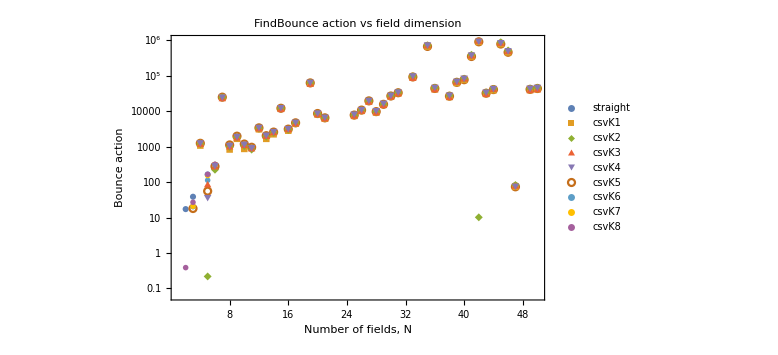

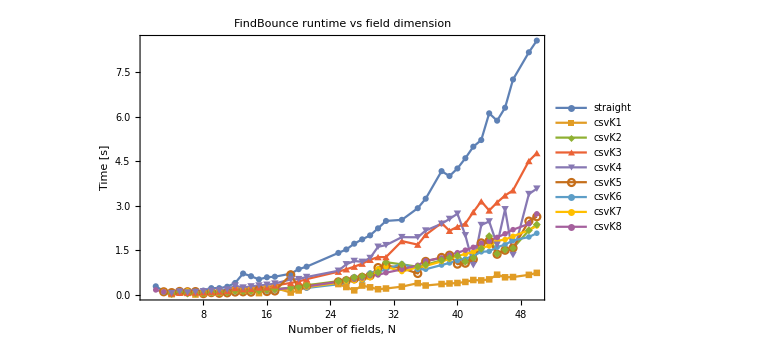

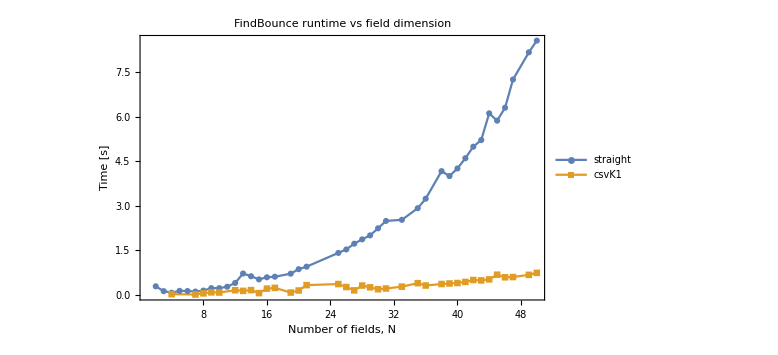

```mathematica
file="findbounce_csvK_scan_results.csv";
raw=Import[file,"CSV"];

head=raw[[1]];
rows=AssociationThread[head->#]&/@raw[[2;;]];

clean[x_]:=StringReplace[ToString[x],"\""->""];
num[x_]:=Quiet@Check[ToExpression[clean[x]],Missing["NA"]];

data=Association[#,"n"->num[#["nphi"]],"method2"->clean[#["method"]],"status2"->clean[#["status"]],"action"->num[#["ActionFindBounceD4"]],"time"->num[#["TimeSeconds"]]]&/@rows;

good=Select[data,#["status2"]=="ok"&&NumberQ[#["n"]]&&NumberQ[#["time"]]&];

methods={"straight","csvK1","csvK2","csvK3","csvK4","csvK5","csvK6","csvK7","csvK8"};

series[col_,m_]:=SortBy[({#["n"],#[col]}&/@Select[good,#["method2"]==m&&NumberQ[#[col]]&]),First];

pAction=ListLogPlot[series["action",#]&/@methods,PlotLegends->Placed[methods,Right],Frame->True,FrameLabel->{"Number of fields, N","Bounce action"},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large,PlotLabel->"FindBounce action vs field dimension"];

pTime=ListLinePlot[series["time",#]&/@methods,PlotLegends->Placed[methods,Right],Frame->True,FrameLabel->{"Number of fields, N","Time [s]"},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large,PlotLabel->"FindBounce runtime vs field dimension"];

methods2 = {"straight","csvK1"};
pTime2=ListLinePlot[series["time",#]&/@methods2,PlotLegends->Placed[methods,Right],Frame->True,FrameLabel->{"Number of fields, N","Time [s]"},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large,PlotLabel->"FindBounce runtime vs field dimension"];

pAction
pTime
pTime2

plotDir=FileNameJoin[{NotebookDirectory[],"Plots"}];
If[!DirectoryQ[plotDir],CreateDirectory[plotDir]];

Export[FileNameJoin[{plotDir,"findbounce_csvK_action_vs_N.png"}],pAction];
Export[FileNameJoin[{plotDir,"findbounce_csvK_time_vs_N.png"}],pTime];
Export[FileNameJoin[{plotDir,"findbounce_csvK_time_vs_1.png"}],pTime2];
```